### Expressions for EPR in extrinsically varying cellular populations

```mathematica
EPR = ((ρon-ρoff)σon σoff)/((σon+σoff)(e+σon+σoff))Log[ρon/ρoff]/.{ρon->B σoff};
```

```mathematica
ExtNoisePdf=FullSimplify[PDF[GammaDistribution[α,1/β],x],x>0]//FullSimplify
```

(ⅇ^(-x β) x^(-1+α) (1/β)^-α)/Gamma[α]

```mathematica
Mean[GammaDistribution[α,1/β]]
```

α/β

```mathematica
Variance[GammaDistribution[α,1/β]]
```

α/β^2

```mathematica
ParsToMoms=Solve[{α/β==m,α/β^2==v},{α,β}][[1]]
```

{α→m^2/v,β→m/v}

```mathematica
Solve[(ρon)Log[ρon/ρoff]==(β Qd Σ(Σ+d))/(σon σoff),ρon]//FullSimplify//Quiet
```

{{ρon→ⅇ^ProductLog[(Qd β Σ (d+Σ))/(ρoff σoff σon)] ρoff}}

```mathematica
ⅇ^Log[(Qd β Σ (d+Σ))/(ρoff σon σoff)] ρoff
```

(Qd β Σ (d+Σ))/(σoff σon)

#### Noise on B

```mathematica
expρon=FullSimplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->B] EPR ⅆB,Re[α]>0&&Re[β]>0]
```

(σoff σon (σoff+(β ρoff-α σoff) (Log[β]-Log[σoff/ρoff])+(-β ρoff+α σoff) PolyGamma[0,α]))/(β (σoff+σon) (e+σoff+σon))

```mathematica
TeXForm[expρon/.{ρon->Subscript[ρ, on],ρoff->Subscript[ρ, off],σoff->Subscript[σ, off],σon->Subscript[σ, on]}//FullSimplify]
```

\frac{\sigma _{\text{off}} \sigma _{\text{on}} \left(\left(\beta  \rho _{\text{off}}-\alpha  \sigma _{\text{off}}\right) \left(-\psi ^{(0)}(\alpha )+\log (\beta )-\log \left(\frac{\sigma _{\text{off}}}{\rho _{\text{off}}}\right)\right)+\sigma _{\text{off}}\right)}{\beta  \left(\sigma _{\text{off}}+\sigma _{\text{on}}\right) \left(e+\sigma _{\text{off}}+\sigma _{\text{on}}\right)}

```mathematica
diffB=(expρon-EPR)/EPR/.B->α/β//FullSimplify
```

-(σoff+(β ρoff-α σoff) (Log[β]-Log[σoff/ρoff]+Log[(α σoff)/(β ρoff)])+(-β ρoff+α σoff) PolyGamma[0,α])/((β ρoff-α σoff) Log[(α σoff)/(β ρoff)])

```mathematica
diffBMoms=diffB/.ParsToMoms//FullSimplify
```

(v σoff+m (ρoff-m σoff) (Log[m/v]-Log[σoff/ρoff]+Log[(m σoff)/ρoff])+m (-ρoff+m σoff) PolyGamma[0,m^2/v])/(m (-ρoff+m σoff) Log[(m σoff)/ρoff])

```mathematica
diffBMomsVeqM=diffρonMoms/.v->m//FullSimplify
```

(σoff+(ρoff-m σoff) (-Log[σoff/ρoff]+Log[(m σoff)/ρoff])+(-ρoff+m σoff) PolyGamma[0,m])/((-ρoff+m σoff) Log[(m σoff)/ρoff])

```mathematica
parsBChangingσoff={
{σoff->0.1,ρoff->10^-1,m->10},{σoff->1,ρoff->10^-1,m->10},{σoff->10,ρoff->10^-1,m->10}}
```

{{σoff→0.1,ρoff→1/10,m→10},{σoff→1,ρoff→1/10,m→10},{σoff→10,ρoff→1/10,m→10}}

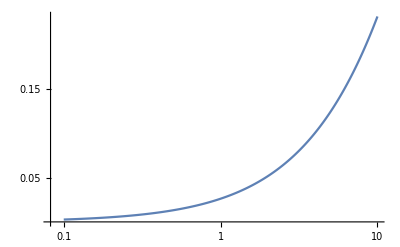

```mathematica
ListPlot[Table[{v/m,diffBMoms}/.parsBChangingσoff[[1]],{v,1,100,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

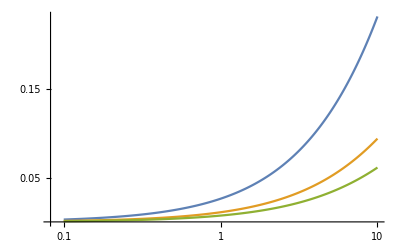

```mathematica
ListPlot[Table[Table[{v/m,diffBMoms}/.parsBChangingσoff[[i]],{v,1,100,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

Note, variation of ρoff can have large effects on the effect of extrinsic noise on ρon on the EPR bound. This could provide a potential reason for having genes which switch off. It contrasts against the no extrinsic noise case since there increasing ρoff only acts to decrease the EPR. However the difference is not a function of other parameters!

```mathematica
σoffvals = Table[σoff->10^x,{x,-2,2,1/(20)}];
```

```mathematica
mBvals = Table[m->10^x,{x,0,2,1/30}];
```

```mathematica
dataσoffmExtB=Flatten[Table[Table[{σoff,m,diffBMoms}//.{v->m,σoffvals[[i]],mBvals[[j]],ρoff->1/1000},{i,1,Length[σoffvals]}],{j,1,Length[mBvals]}],1];
```

```mathematica
dataσoffmExtB//N;
```

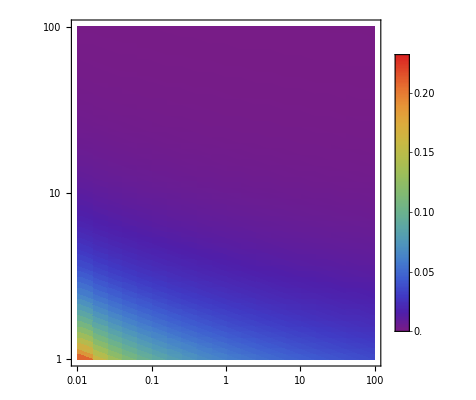

```mathematica
ListDensityPlot[dataσoffmExtB//N,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[dataσoffmExtB[[All,3]]],Max[dataσoffmExtB[[All,3]]]}}],ScalingFunctions->{"Log","Log"}]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\B_hm.csv",dataσoffmExtB//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\B_hm.csv

```mathematica
{Bp1,Bp2,Bp3}=Table[Table[{v/m,diffBMoms}/.parsBChangingσoff[[i]]//N,{v,1,100,1/10}],{i,1,3}];
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\rho_b_p1.csv",Bp1//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\rho_b_p2.csv",Bp2//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\rho_b_p3.csv",Bp3//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\rho_b_p1.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\rho_b_p2.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\rho_b_p3.csv

#### Noise on σoff

```mathematica
expσoff=Simplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->σoff] EPR ⅆσoff,α>0&&β>0&&B>0&&ρoff>0&&σon>0&&e>0]
```

1/(e α (1+α) Gamma[α])β^α σon (-B ⅇ^(β σon) π α σon^(1+α) Csc[π α]-B ⅇ^(β σon) π (1+α) σon^(1+α) Csc[π α]+B e ⅇ^(β (e+σon)) π α (e+σon)^α Csc[π α]+B e ⅇ^(β (e+σon)) π (1+α) (e+σon)^α Csc[π α]+B ⅇ^(β (e+σon)) π α σon (e+σon)^α Csc[π α]+B ⅇ^(β (e+σon)) π (1+α) σon (e+σon)^α Csc[π α]-B ⅇ^(β σon) π^2 α (1+α) σon^(1+α) Cot[π α] Csc[π α]+B e ⅇ^(β (e+σon)) π^2 α (1+α) (e+σon)^α Cot[π α] Csc[π α]+B ⅇ^(β (e+σon)) π^2 α (1+α) σon (e+σon)^α Cot[π α] Csc[π α]+B ⅇ^(β σon) (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon]+2 B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon]-B e ⅇ^(β (e+σon)) (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-2 B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-B ⅇ^(β (e+σon)) (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-2 B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[α] Gamma[-α,β σon]+ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[α] Gamma[-α,β (e+σon)]-B ⅇ^(β σon) π α σon^(1+α) Csc[π α] Log[B/ρoff]-B ⅇ^(β σon) π α^2 σon^(1+α) Csc[π α] Log[B/ρoff]+B ⅇ^(β σon) π α (1+α) σon^(1+α) Csc[π α] Log[B/ρoff]+B e ⅇ^(β (e+σon)) π α (e+σon)^α Csc[π α] Log[B/ρoff]+B e ⅇ^(β (e+σon)) π α^2 (e+σon)^α Csc[π α] Log[B/ρoff]-B e ⅇ^(β (e+σon)) π α (1+α) (e+σon)^α Csc[π α] Log[B/ρoff]+B ⅇ^(β (e+σon)) π α σon (e+σon)^α Csc[π α] Log[B/ρoff]+B ⅇ^(β (e+σon)) π α^2 σon (e+σon)^α Csc[π α] Log[B/ρoff]-B ⅇ^(β (e+σon)) π α (1+α) σon (e+σon)^α Csc[π α] Log[B/ρoff]+B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[B/ρoff]+B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[B/ρoff]-B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] Gamma[-α,β σon] Log[B/ρoff]+ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] Gamma[-α,β (e+σon)] Log[B/ρoff]-B ⅇ^(β σon) π α σon^(1+α) Csc[π α] Log[σon]-B ⅇ^(β σon) π α^2 σon^(1+α) Csc[π α] Log[σon]+B ⅇ^(β σon) π α (1+α) σon^(1+α) Csc[π α] Log[σon]+B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[σon]+B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[σon]-ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] Gamma[-α,β σon] Log[σon]-B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[β σon]-B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[β σon]+ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] Gamma[-α,β σon] Log[β σon]+B e ⅇ^(β (e+σon)) π α (e+σon)^α Csc[π α] Log[e+σon]+B e ⅇ^(β (e+σon)) π α^2 (e+σon)^α Csc[π α] Log[e+σon]-B e ⅇ^(β (e+σon)) π α (1+α) (e+σon)^α Csc[π α] Log[e+σon]+B ⅇ^(β (e+σon)) π α σon (e+σon)^α Csc[π α] Log[e+σon]+B ⅇ^(β (e+σon)) π α^2 σon (e+σon)^α Csc[π α] Log[e+σon]-B ⅇ^(β (e+σon)) π α (1+α) σon (e+σon)^α Csc[π α] Log[e+σon]-B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]-B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]-B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]-B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]+ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] Gamma[-α,β (e+σon)] Log[e+σon]+B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]+B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]+B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]+B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]-ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] Gamma[-α,β (e+σon)] Log[β (e+σon)]-B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β σon]-B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β σon]+B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-α},{}},β σon]-ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-α},{}},β (e+σon)]+B ⅇ^(β σon) π α (1+α) (σon^(1+α)-ⅇ^(e β) (e+σon)^(1+α)) Csc[π α] PolyGamma[0,-1-α]-ⅇ^(β σon) α (1+α) (B π (σon^(1+α)-e ⅇ^(e β) (e+σon)^α-ⅇ^(e β) σon (e+σon)^α) Csc[π α]+Gamma[1+α] (-B (1+α) σon^(1+α) Gamma[-1-α,β σon]+B ⅇ^(e β) (1+α) (e+σon)^(1+α) Gamma[-1-α,β (e+σon)]+ρoff (σon^α Gamma[-α,β σon]-ⅇ^(e β) (e+σon)^α Gamma[-α,β (e+σon)]))) PolyGamma[0,α])

```mathematica
expσoff=1/(e α (1+α) Gamma[α])β^α σon (-B ⅇ^(β σon) π α σon^(1+α) Csc[π α]-B ⅇ^(β σon) π (1+α) σon^(1+α) Csc[π α]+B e ⅇ^(β (e+σon)) π α (e+σon)^α Csc[π α]+B e ⅇ^(β (e+σon)) π (1+α) (e+σon)^α Csc[π α]+B ⅇ^(β (e+σon)) π α σon (e+σon)^α Csc[π α]+B ⅇ^(β (e+σon)) π (1+α) σon (e+σon)^α Csc[π α]-B ⅇ^(β σon) π^2 α (1+α) σon^(1+α) Cot[π α] Csc[π α]+B e ⅇ^(β (e+σon)) π^2 α (1+α) (e+σon)^α Cot[π α] Csc[π α]+B ⅇ^(β (e+σon)) π^2 α (1+α) σon (e+σon)^α Cot[π α] Csc[π α]+B ⅇ^(β σon) (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon]+2 B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon]-B e ⅇ^(β (e+σon)) (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-2 B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-B ⅇ^(β (e+σon)) (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-2 B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[α] Gamma[-α,β σon]+ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[α] Gamma[-α,β (e+σon)]-B ⅇ^(β σon) π α σon^(1+α) Csc[π α] Log[B/ρoff]-B ⅇ^(β σon) π α^2 σon^(1+α) Csc[π α] Log[B/ρoff]+B ⅇ^(β σon) π α (1+α) σon^(1+α) Csc[π α] Log[B/ρoff]+B e ⅇ^(β (e+σon)) π α (e+σon)^α Csc[π α] Log[B/ρoff]+B e ⅇ^(β (e+σon)) π α^2 (e+σon)^α Csc[π α] Log[B/ρoff]-B e ⅇ^(β (e+σon)) π α (1+α) (e+σon)^α Csc[π α] Log[B/ρoff]+B ⅇ^(β (e+σon)) π α σon (e+σon)^α Csc[π α] Log[B/ρoff]+B ⅇ^(β (e+σon)) π α^2 σon (e+σon)^α Csc[π α] Log[B/ρoff]-B ⅇ^(β (e+σon)) π α (1+α) σon (e+σon)^α Csc[π α] Log[B/ρoff]+B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[B/ρoff]+B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[B/ρoff]-B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] Gamma[-α,β σon] Log[B/ρoff]+ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] Gamma[-α,β (e+σon)] Log[B/ρoff]-B ⅇ^(β σon) π α σon^(1+α) Csc[π α] Log[σon]-B ⅇ^(β σon) π α^2 σon^(1+α) Csc[π α] Log[σon]+B ⅇ^(β σon) π α (1+α) σon^(1+α) Csc[π α] Log[σon]+B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[σon]+B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[σon]-ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] Gamma[-α,β σon] Log[σon]-B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[β σon]-B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[β σon]+ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] Gamma[-α,β σon] Log[β σon]+B e ⅇ^(β (e+σon)) π α (e+σon)^α Csc[π α] Log[e+σon]+B e ⅇ^(β (e+σon)) π α^2 (e+σon)^α Csc[π α] Log[e+σon]-B e ⅇ^(β (e+σon)) π α (1+α) (e+σon)^α Csc[π α] Log[e+σon]+B ⅇ^(β (e+σon)) π α σon (e+σon)^α Csc[π α] Log[e+σon]+B ⅇ^(β (e+σon)) π α^2 σon (e+σon)^α Csc[π α] Log[e+σon]-B ⅇ^(β (e+σon)) π α (1+α) σon (e+σon)^α Csc[π α] Log[e+σon]-B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]-B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]-B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]-B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]+ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] Gamma[-α,β (e+σon)] Log[e+σon]+B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]+B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]+B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]+B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]-ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] Gamma[-α,β (e+σon)] Log[β (e+σon)]-B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β σon]-B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β σon]+B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-α},{}},β σon]-ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-α},{}},β (e+σon)]+B ⅇ^(β σon) π α (1+α) (σon^(1+α)-ⅇ^(e β) (e+σon)^(1+α)) Csc[π α] PolyGamma[0,-1-α]-ⅇ^(β σon) α (1+α) (B π (σon^(1+α)-e ⅇ^(e β) (e+σon)^α-ⅇ^(e β) σon (e+σon)^α) Csc[π α]+Gamma[1+α] (-B (1+α) σon^(1+α) Gamma[-1-α,β σon]+B ⅇ^(e β) (1+α) (e+σon)^(1+α) Gamma[-1-α,β (e+σon)]+ρoff (σon^α Gamma[-α,β σon]-ⅇ^(e β) (e+σon)^α Gamma[-α,β (e+σon)]))) PolyGamma[0,α]);
```

```mathematica
diffσoff=(expσoff-EPR)/EPR/.σoff->α/β//Simplify
```

1/(α (B α-β ρoff) σon Log[(B α)/(β ρoff)])β^2 (α/β+σon) (e+α/β+σon) (-(α (B α-β ρoff) σon Log[(B α)/(β ρoff)])/((α+β σon) (α+β (e+σon)))+1/(e α (1+α) Gamma[α])β^α σon (-B ⅇ^(β σon) π α σon^(1+α) Csc[π α]-B ⅇ^(β σon) π (1+α) σon^(1+α) Csc[π α]+B e ⅇ^(β (e+σon)) π α (e+σon)^α Csc[π α]+B e ⅇ^(β (e+σon)) π (1+α) (e+σon)^α Csc[π α]+B ⅇ^(β (e+σon)) π α σon (e+σon)^α Csc[π α]+B ⅇ^(β (e+σon)) π (1+α) σon (e+σon)^α Csc[π α]-B ⅇ^(β σon) π^2 α (1+α) σon^(1+α) Cot[π α] Csc[π α]+B e ⅇ^(β (e+σon)) π^2 α (1+α) (e+σon)^α Cot[π α] Csc[π α]+B ⅇ^(β (e+σon)) π^2 α (1+α) σon (e+σon)^α Cot[π α] Csc[π α]+B ⅇ^(β σon) (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon]+2 B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon]-B e ⅇ^(β (e+σon)) (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-2 B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-B ⅇ^(β (e+σon)) (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-2 B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)]-ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[α] Gamma[-α,β σon]+ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[α] Gamma[-α,β (e+σon)]-B ⅇ^(β σon) π α σon^(1+α) Csc[π α] Log[B/ρoff]-B ⅇ^(β σon) π α^2 σon^(1+α) Csc[π α] Log[B/ρoff]+B ⅇ^(β σon) π α (1+α) σon^(1+α) Csc[π α] Log[B/ρoff]+B e ⅇ^(β (e+σon)) π α (e+σon)^α Csc[π α] Log[B/ρoff]+B e ⅇ^(β (e+σon)) π α^2 (e+σon)^α Csc[π α] Log[B/ρoff]-B e ⅇ^(β (e+σon)) π α (1+α) (e+σon)^α Csc[π α] Log[B/ρoff]+B ⅇ^(β (e+σon)) π α σon (e+σon)^α Csc[π α] Log[B/ρoff]+B ⅇ^(β (e+σon)) π α^2 σon (e+σon)^α Csc[π α] Log[B/ρoff]-B ⅇ^(β (e+σon)) π α (1+α) σon (e+σon)^α Csc[π α] Log[B/ρoff]+B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[B/ρoff]+B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[B/ρoff]-B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[B/ρoff]-ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] Gamma[-α,β σon] Log[B/ρoff]+ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] Gamma[-α,β (e+σon)] Log[B/ρoff]-B ⅇ^(β σon) π α σon^(1+α) Csc[π α] Log[σon]-B ⅇ^(β σon) π α^2 σon^(1+α) Csc[π α] Log[σon]+B ⅇ^(β σon) π α (1+α) σon^(1+α) Csc[π α] Log[σon]+B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[σon]+B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[σon]-ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] Gamma[-α,β σon] Log[σon]-B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[β σon]-B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] Gamma[-1-α,β σon] Log[β σon]+ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] Gamma[-α,β σon] Log[β σon]+B e ⅇ^(β (e+σon)) π α (e+σon)^α Csc[π α] Log[e+σon]+B e ⅇ^(β (e+σon)) π α^2 (e+σon)^α Csc[π α] Log[e+σon]-B e ⅇ^(β (e+σon)) π α (1+α) (e+σon)^α Csc[π α] Log[e+σon]+B ⅇ^(β (e+σon)) π α σon (e+σon)^α Csc[π α] Log[e+σon]+B ⅇ^(β (e+σon)) π α^2 σon (e+σon)^α Csc[π α] Log[e+σon]-B ⅇ^(β (e+σon)) π α (1+α) σon (e+σon)^α Csc[π α] Log[e+σon]-B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]-B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]-B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]-B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[e+σon]+ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] Gamma[-α,β (e+σon)] Log[e+σon]+B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]+B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]+B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]+B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] Gamma[-1-α,β (e+σon)] Log[β (e+σon)]-ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] Gamma[-α,β (e+σon)] Log[β (e+σon)]-B ⅇ^(β σon) α (1+α) σon^(1+α) Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β σon]-B ⅇ^(β σon) α^2 (1+α) σon^(1+α) Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β σon]+B e ⅇ^(β (e+σon)) α (1+α) (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+B e ⅇ^(β (e+σon)) α^2 (1+α) (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+B ⅇ^(β (e+σon)) α (1+α) σon (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+B ⅇ^(β (e+σon)) α^2 (1+α) σon (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-1-α},{}},β (e+σon)]+ⅇ^(β σon) α (1+α) ρoff σon^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-α},{}},β σon]-ⅇ^(β (e+σon)) α (1+α) ρoff (e+σon)^α Gamma[1+α] MeijerG[{{},{1,1}},{{0,0,-α},{}},β (e+σon)]+B ⅇ^(β σon) π α (1+α) (σon^(1+α)-ⅇ^(e β) (e+σon)^(1+α)) Csc[π α] PolyGamma[0,-1-α]-ⅇ^(β σon) α (1+α) (B π (σon^(1+α)-e ⅇ^(e β) (e+σon)^α-ⅇ^(e β) σon (e+σon)^α) Csc[π α]+Gamma[1+α] (-B (1+α) σon^(1+α) Gamma[-1-α,β σon]+B ⅇ^(e β) (1+α) (e+σon)^(1+α) Gamma[-1-α,β (e+σon)]+ρoff (σon^α Gamma[-α,β σon]-ⅇ^(e β) (e+σon)^α Gamma[-α,β (e+σon)]))) PolyGamma[0,α]))

```mathematica
diffσoffMoms=diffσoff/.ParsToMoms;
```

```mathematica
diffσoffMoms/.{σon->10,B->11,ρoff->1/100,e->1,m->10,v->12}//N
```

-0.0198006

```mathematica
diffσoffMoms/.{σon->10,B->20,ρoff->1/100,e->1,m->10,v->12}//N
```

-0.0201867

```mathematica
diffσoffMoms/.{σon->15,B->20,ρoff->1/100,e->1,m->10,v->12}//N
```

0.0228608

```mathematica
diffσoffMoms/.{σon->10,B->11,ρoff->1/100,e->10,m->10,v->12}//N
```

0.670448

This is not a function of ρon or ρoff!

```mathematica
parsσoff1={σon->10,ρon->20,ρoff->0.1,d->1,m->1}
```

```mathematica
{σon->10,ρon->20,ρoff->0.1,d->1,m->1}
```

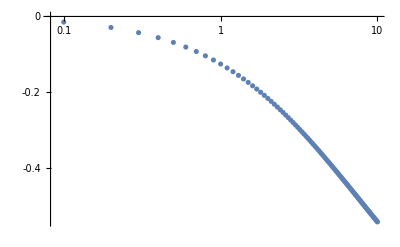

```mathematica
ListPlot[Table[{v/m,diffσoffMoms}/.parsσoff1,{v,1/10,10,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

```mathematica
parsσoff2={σon->10,ρon->20,ρoff->0.1,d->1,m->10}
```

```mathematica
{σon->10,ρon->20,ρoff->0.1,d->1,m->10}
```

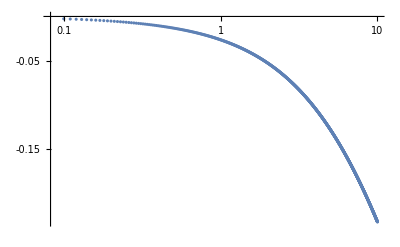

```mathematica
ListPlot[Table[{v/m,diffσoffMoms}/.parsσoff2,{v,1,100,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

```mathematica
parsσoff3={σon->10,ρon->20,ρoff->0.1,d->1,m->100}
```

```mathematica
{σon->10,ρon->20,ρoff->0.1,d->1,m->100}
```

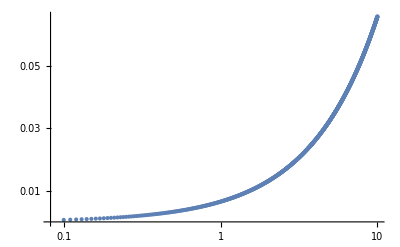

```mathematica
ListPlot[Table[{v/m,diffσoffMoms}/.parsσoff3,{v,10,1000,1}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

```mathematica
parsσoffChangingd={{σon->3,ρon->20,ρoff->0.1,d->0.1,m->10},{σon->3,ρon->20,ρoff->0.1,d->1,m->10},{σon->3,ρon->20,ρoff->0.1,d->10,m->10}}
```

```mathematica
{{σon->3,ρon->20,ρoff->0.1,d->0.1,m->10},{σon->3,ρon->20,ρoff->0.1,d->1,m->10},{σon->3,ρon->20,ρoff->0.1,d->10,m->10}}
```

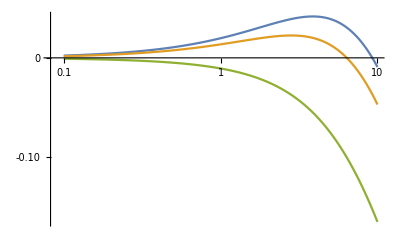

```mathematica
ListPlot[Table[Table[{v/m,diffσoffMoms}/.parsσoffChangingd[[i]],{v,1,100,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

```mathematica
diffσoffMoms//.v->1*m//.parsσoffChangingσon[[1]]//N
```

0.0529516

Implications for the variation of the burst frequency in the population.

```mathematica
dvals = Table[d->10^x,{x,-1,1,1/(30)}];
```

```mathematica
mσoffvals = Table[m->10^x,{x,-2,2,1/(30)}];
```

```mathematica
datadmExtσoff=Flatten[Table[Table[{d,m,diffσoffMoms}//.{v->m,dvals[[i]],mσoffvals[[j]],σon->1},{i,1,Length[dvals]}],{j,1,Length[mσoffvals]}],1]//N;
```

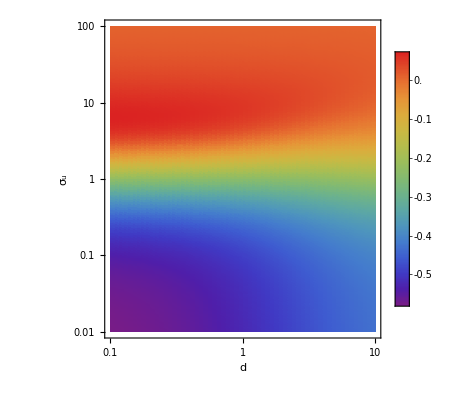

```mathematica
ListDensityPlot[datadmExtσoff,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[datadmExtσoff[[All,3]]],Max[datadmExtσoff[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"d","σ_u"}]
```

```mathematica
datadmExtσoff2=Flatten[Table[Table[{d,m,diffσoffMoms}//.{v->m,dvals[[i]],mσoffvals[[j]],σon->100},{i,1,Length[dvals]}],{j,1,Length[mσoffvals]}],1]//N;
```

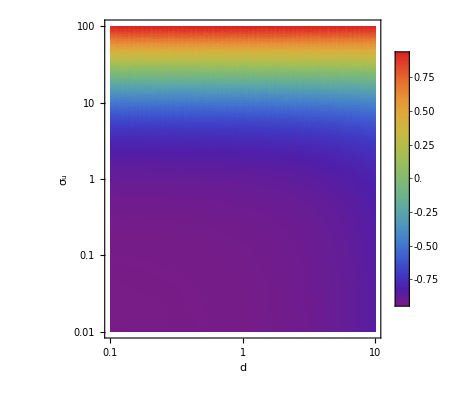

```mathematica
ListDensityPlot[datadmExtσoff2,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[datadmExtσoff[[All,3]]],Max[datadmExtσoff[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"d","σ_u"}]
```

```mathematica
Max[datadmExtσoff[[All,3]]]
```

0.0657874

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\sigma_u_hm.csv",datadmExtσoff//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\sigma_u_hm.csv

```mathematica
Min[{σoffp1,σoffp2,σoffp3}//Flatten]
```

-0.164738

```mathematica
{σoffp1,σoffp2,σoffp3}=Table[Table[{v/m,diffσoffMoms}/.parsσoffChangingd[[i]],{v,1,100,1/10}],{i,1,3}]//N//Quiet
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\sigma_u_p1.csv",σoffp1//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\sigma_u_p2.csv",σoffp2//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\sigma_u_p3.csv",σoffp3//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\sigma_u_p1.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\sigma_u_p2.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\sigma_u_p3.csv

#### Noise on d

```mathematica
expd=FullSimplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->d] EPR ⅆd,α>0&&β>0&&ρon>0&&ρoff>0&&σon>0&&d>0&&(σoff∉Reals&&σoff≠Re[σoff])||σon+Re[σoff]>0]
```

```mathematica
ConditionalExpression[ⅇ^(β (σon+σoff)) β^α (ρon-ρoff) σon σoff (σon+σoff)^(-2+α) Gamma[1-α,β (σon+σoff)] Log[ρon/ρoff], Re[α]>0&&Re[β]>0&&((σoff∉Reals&&Im[σoff]≠0)||σon+Re[σoff]>0)]
```

```mathematica
EPR
```

```mathematica
((ρon-ρoff) σon σoff Log[ρon/ρoff])/((σon+σoff) (d+σon+σoff))
```

```mathematica
diffd=FullSimplify[(expd-EPR)/EPR/.d->α/β//FullSimplify,σon>0&&σoff>0&&Re[α]>0&&Re[β]>0]
```

```mathematica
-1+ⅇ^(β (σon+σoff)) (α+β (σon+σoff)) ExpIntegralE[α,β (σon+σoff)]
```

```mathematica
TeXForm[-1+ⅇ^(β (σon+σoff)) β (m+σon+σoff) ExpIntegralE[α,β (σon+σoff)]]
```

\beta  e^{\beta  (\text{$\sigma $b}+\text{$\sigma $u})} (m+\text{$\sigma $b}+\text{$\sigma $u})
   E_{\alpha }(\beta  (\text{$\sigma $b}+\text{$\sigma $u}))-1

This is not a function of ρon or ρoff!

```mathematica
diffdMoms=diffd/.ParsToMoms//FullSimplify
```

```mathematica
-1+(ⅇ^((m (σon+σoff))/v) m (m+σon+σoff) ExpIntegralE[m^2/v,(m (σon+σoff))/v])/v
```

```mathematica
parsdChangingσoff={{σon->1,ρon->20,ρoff->0.1,σoff->1,m->1},{σon->1,ρon->20,ρoff->0.1,σoff->10,m->1},{σon->1,ρon->20,ρoff->0.1,σoff->100,m->1}}
```

```mathematica
{{σon->1,ρon->20,ρoff->0.1,σoff->1,m->1},{σon->1,ρon->20,ρoff->0.1,σoff->10,m->1},{σon->1,ρon->20,ρoff->0.1,σoff->100,m->1}}
```

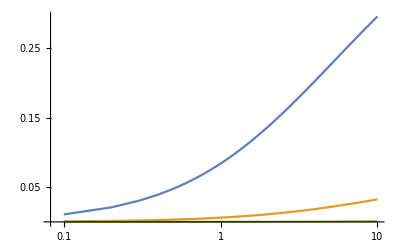

```mathematica
ListPlot[Table[Table[{v/m,diffdMoms}/.parsdChangingσoff[[i]],{v,1/10,10,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

```mathematica
SetPrecision[Table[{v/m,diffdMoms}/.parsdChangingσoff[[3]],{v,1/10,10,1/10}],1000]//N
```

{{0.1,9.59317×10^-6},{0.2,0.0000191495},{0.3,0.0000286694},{0.4,0.000038153},{0.5,0.0000476008},{0.6,0.000057013},{0.7,0.0000663898},{0.8,0.0000757317},{0.9,0.0000850389},{1.,0.0000943116},{1.1,0.00010355},{1.2,0.000112755},{1.3,0.000121926},{1.4,0.000131064},{1.5,0.000140168},{1.6,0.00014924},{1.7,0.00015828},{1.8,0.000167287},{1.9,0.000176262},{2.,0.000185205},{2.1,0.000194117},{2.2,0.000202997},{2.3,0.000211846},{2.4,0.000220665},{2.5,0.000229452},{2.6,0.00023821},{2.7,0.000246937},{2.8,0.000255634},{2.9,0.000264302},{3.,0.00027294},{3.1,0.000281549},{3.2,0.000290129},{3.3,0.000298679},{3.4,0.000307202},{3.5,0.000315695},{3.6,0.000324161},{3.7,0.000332598},{3.8,0.000341008},{3.9,0.00034939},{4.,0.000357744},{4.1,0.000366072},{4.2,0.000374372},{4.3,0.000382645},{4.4,0.000390891},{4.5,0.000399111},{4.6,0.000407305},{4.7,0.000415472},{4.8,0.000423614},{4.9,0.000431729},{5.,0.000439819},{5.1,0.000447884},{5.2,0.000455923},{5.3,0.000463937},{5.4,0.000471926},{5.5,0.00047989},{5.6,0.000487829},{5.7,0.000495744},{5.8,0.000503635},{5.9,0.000511501},{6.,0.000519343},{6.1,0.000527162},{6.2,0.000534956},{6.3,0.000542728},{6.4,0.000550475},{6.5,0.0005582},{6.6,0.000565901},{6.7,0.000573579},{6.8,0.000581234},{6.9,0.000588867},{7.,0.000596477},{7.1,0.000604065},{7.2,0.00061163},{7.3,0.000619173},{7.4,0.000626694},{7.5,0.000634193},{7.6,0.00064167},{7.7,0.000649126},{7.8,0.00065656},{7.9,0.000663973},{8.,0.000671364},{8.1,0.000678734},{8.2,0.000686084},{8.3,0.000693412},{8.4,0.00070072},{8.5,0.000708007},{8.6,0.000715273},{8.7,0.000722519},{8.8,0.000729745},{8.9,0.00073695},{9.,0.000744135},{9.1,0.000751301},{9.2,0.000758446},{9.3,0.000765572},{9.4,0.000772678},{9.5,0.000779765},{9.6,0.000786832},{9.7,0.00079388},{9.8,0.000800909},{9.9,0.000807918},{10.,0.000814909}}

For m=v plot heat map of mean of d vs σon.

```mathematica
σoffvals = Table[σoff->10^x,{x,-2,2,1/(30)}];
```

```mathematica
mdvals = Table[m->10^x,{x,-1,1,1/(30)}];
```

```mathematica
dataσoffmExtd=Flatten[Table[Table[{σoff,m,diffdMoms}//.{v->m,σoffvals[[i]],mdvals[[j]],σon->10},{i,1,Length[σoffvals]}],{j,1,Length[mdvals]}],1]//N;
```

```mathematica
dataσoffmExtd;
```

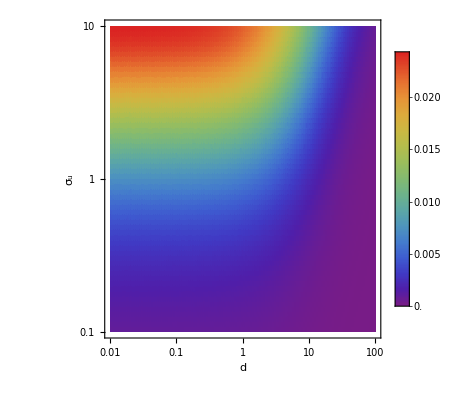

```mathematica
ListDensityPlot[dataσoffmExtd,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[dataσoffmExtd[[All,3]]],Max[dataσoffmExtd[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"d","σ_u"}]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\d_hm.csv",dataσoffmExtd//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\d_hm.csv

```mathematica
Min[{dp1,dp2,dp3}//Flatten]
```

9.59317×10^-6

```mathematica
{dp1,dp2,dp3}=Table[SetPrecision[Table[{v/m,diffdMoms}/.parsdChangingσoff[[i]],{v,1/10,10,1/10}],1000],{i,1,3}]//N//Quiet;
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\d_p1.csv",dp1//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\d_p2.csv",dp2//N]
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\ext-plots\\d_p3.csv",dp3[[1;;]]//N]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\d_p1.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\d_p2.csv

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\ext-plots\d_p3.csv

#### Noise on ρoff

```mathematica
expρoff=FullSimplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->ρoff] EPR ⅆρoff,α>0&&β>0&&ρon>0&&ρoff>0&&σon>0&&d>0]
```

```mathematica
(σon σoff (1+(-α+β ρon) Log[β ρon]+(α-β ρon) PolyGamma[0,α]))/(β (σon+σoff) (d+σon+σoff))
```

```mathematica
TeXForm[expρoff/.{ρon->Subscript[ρ, b],ρoff->Subscript[ρ, u],σoff->Subscript[σ, u],σon->Subscript[σ, b]}//FullSimplify]
```

\frac{\sigma _b \sigma _u \left(\left(\beta  \rho _b-\alpha \right) \log \left(\beta  \rho _b\right)+\psi ^{(0)}(\alpha ) \left(\alpha -\beta  \rho _b\right)+1\right)}{\beta  \left(\sigma _b+\sigma _u\right) \left(\sigma
   _b+d+\sigma _u\right)}

```mathematica
diffρoff=FullSimplify[(expρoff-EPR)/EPR/.ρoff->α/β//FullSimplify,σon>0&&σoff>0&&Re[α]>0&&Re[β]>0]
```

```mathematica
(-1+(α-β ρon) (Log[β ρon]-Log[(β ρon)/α])+(-α+β ρon) PolyGamma[0,α])/((α-β ρon) Log[(β ρon)/α])
```

```mathematica
diffρoffMoms=diffρoff/.ParsToMoms//FullSimplify
```

```mathematica
(-v+m (m-ρon) (-Log[ρon/m]+Log[(m ρon)/v])+m (-m+ρon) PolyGamma[0,m^2/v])/(m (m-ρon) Log[ρon/m])
```

```mathematica
parsρoffChangingσon={{σon->1,ρon->10.1,d->1,σoff->10,m->10},{σon->1,ρon->50,d->1,σoff->10,m->10},{σon->1,ρon->100,d->1,σoff->10,m->10}}
```

```mathematica
{{σon->1,ρon->10.1,d->1,σoff->10,m->10},{σon->1,ρon->50,d->1,σoff->10,m->10},{σon->1,ρon->100,d->1,σoff->10,m->10}}
```

Variation of parameters in the population

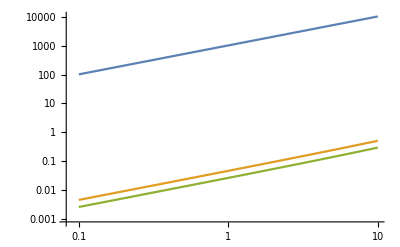

```mathematica
ListPlot[Table[Table[{v/m,diffρoffMoms}/.parsρoffChangingσon[[i]],{v,1,100,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Log"},Joined->True]
```

Bigger effect for larger ρoff too! Play with this. For m=v plot heat map of mean of ρoff vs σon.

```mathematica
ρonvals = Table[ρon->10^x,{x,1001/1000,2,1/(2*11)}];
```

```mathematica
mρoffvals = Table[m->10^x,{x,-1,1,1}];
```

```mathematica
dataρonmExtρoff=Flatten[Table[Table[{ρon,m,diffρoffMoms}//.{v->m,ρonvals[[i]],mρoffvals[[j]],σon->1},{i,1,Length[ρonvals]}],{j,1,Length[mρoffvals]}],1]//N;
```

```mathematica
dataρonmExtρoff
```

{{10.0231,0.1,1.78448},{11.129,0.1,1.7427},{12.3569,0.1,1.70295},{13.7203,0.1,1.66507},{15.2341,0.1,1.62894},{16.915,0.1,1.59442},{18.7814,0.1,1.56141},{20.8536,0.1,1.52981},{23.1546,0.1,1.49952},{25.7093,0.1,1.47046},{28.546,0.1,1.44255},{31.6957,0.1,1.41572},{35.1929,0.1,1.38991},{39.0759,0.1,1.36506},{43.3874,0.1,1.34112},{48.1746,0.1,1.31802},{53.49,0.1,1.29573},{59.3919,0.1,1.27421},{65.945,0.1,1.2534},{73.2211,0.1,1.23329},{81.3001,0.1,1.21382},{90.2704,0.1,1.19497},{10.0231,1.,0.298515},{11.129,1.,0.280526},{12.3569,1.,0.264603},{13.7203,1.,0.250424},{15.2341,1.,0.237731},{16.915,1.,0.22631},{18.7814,1.,0.215985},{20.8536,1.,0.20661},{23.1546,1.,0.198063},{25.7093,1.,0.190241},{28.546,1.,0.183057},{31.6957,1.,0.176436},{35.1929,1.,0.170314},{39.0759,1.,0.164637},{43.3874,1.,0.159358},{48.1746,1.,0.154436},{53.49,1.,0.149835},{59.3919,1.,0.145524},{65.945,1.,0.141475},{73.2211,1.,0.137665},{81.3001,1.,0.134072},{90.2704,1.,0.130678},{10.0231,10.,18861.5},{11.129,10.,8.75613},{12.3569,10.,2.24507},{13.7203,10.,1.01055},{15.2341,10.,0.574612},{16.915,10.,0.371839},{18.7814,10.,0.261328},{20.8536,10.,0.194529},{23.1546,10.,0.151085},{25.7093,10.,0.121246},{28.546,10.,0.0998658},{31.6957,10.,0.0840196},{35.1929,10.,0.0719457},{39.0759,10.,0.0625313},{43.3874,10.,0.0550455},{48.1746,10.,0.0489923},{53.49,10.,0.0440252},{59.3919,10.,0.0398966},{65.945,10.,0.0364256},{73.2211,10.,0.0334773},{81.3001,10.,0.03095},{90.2704,10.,0.0287654}}

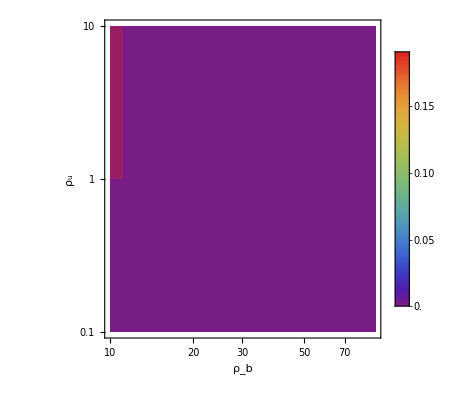

```mathematica
ListDensityPlot[dataρonmExtρoff,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[dataσoffmExtd[[All,3]]],Max[dataσoffmExtd[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"ρ_b","ρ_u"}]
```

### Other stuff

```mathematica
pPDF[n_]:=((ρ/d)^n Exp[-ρ/d])/(n!)
```

```mathematica
Limit[∑_(n=0)^∞ (pPDF[n]r-pPDF[n+1]d(n+1))Log[(pPDF[n]r)/(pPDF[n+1]d(n+1))]//FullSimplify,r->ρ]
```

0

```mathematica
∑_(n=0)^∞ ((ρ/d)^n Exp[-ρ/d])/(n!)Log[((ρ/d)^n Exp[-ρ/d])/(n!)]//FullSimplify
```

∑_(n=0)^∞ (ⅇ^(-ρ/d) (ρ/d)^n Log[(ⅇ^(-ρ/d) (ρ/d)^n)/(n!)])/(n!)

#### Noise on σon

```mathematica
expσoff=FullSimplify[∫_0^∞ Evaluate[ExtNoisePdf/.x->σon] EPR ⅆσon,α>0&&β>0&&ρon>0&&ρoff>0&&σoff>0&&d>0]
```

```mathematica
1/d ⅇ^(β σoff) α (ρon-ρoff) σoff (ExpIntegralE[1+α,β σoff]-ⅇ^(d β) ExpIntegralE[1+α,β (d+σoff)]) Log[ρon/ρoff]
```

```mathematica
diffσoff=(expσoff-EPR)/EPR/.σon->α/β//FullSimplify
```

```mathematica
-1+1/(d β)ⅇ^(β σoff) (α+β σoff) (α+β (d+σoff)) (ExpIntegralE[1+α,β σoff]-ⅇ^(d β) ExpIntegralE[1+α,β (d+σoff)])
```

```mathematica
diffσoffMoms=diffσoff/.ParsToMoms//FullSimplify
```

```mathematica
-1+(ⅇ^((m σoff)/v) m (m+σoff) (d+m+σoff) (ExpIntegralE[(m^2+v)/v,(m σoff)/v]-ⅇ^((d m)/v) ExpIntegralE[(m^2+v)/v,(m (d+σoff))/v]))/(d v)
```

This is not a function of ρon or ρoff!

```mathematica
parsσoff1={σoff->10,ρon->20,ρoff->0.1,d->1,m->1}
```

```mathematica
{σoff->10,ρon->20,ρoff->0.1,d->1,m->1}
```

```mathematica
ListPlot[Table[{v/m,diffσoffMoms}/.parsσoff1,{v,1/10,10,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

```mathematica
parsσoff2={σoff->10,ρon->20,ρoff->0.1,d->1,m->10}
```

```mathematica
{σoff->10,ρon->20,ρoff->0.1,d->1,m->10}
```

```mathematica
ListPlot[Table[{v/m,diffσoffMoms}/.parsσoff2,{v,1,100,1/10}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

```mathematica
parsσoff3={σon->10,ρon->20,ρoff->0.1,d->1,m->100}
```

```mathematica
{σon->10,ρon->20,ρoff->0.1,d->1,m->100}
```

```mathematica
ListPlot[Table[{v/m,diffσoffMoms}/.parsσoff3,{v,10,1000,1}],PlotRange->All,ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

```mathematica
parsσoffChangingd={{σon->3,ρon->20,ρoff->0.1,d->0.1,m->10},{σon->3,ρon->20,ρoff->0.1,d->1,m->10},{σon->3,ρon->20,ρoff->0.1,d->10,m->10}}
```

```mathematica
{{σon->3,ρon->20,ρoff->0.1,d->0.1,m->10},{σon->3,ρon->20,ρoff->0.1,d->1,m->10},{σon->3,ρon->20,ρoff->0.1,d->10,m->10}}
```

```mathematica
ListPlot[Table[Table[{v/m,diffσoffMoms}/.parsσoffChangingd[[i]],{v,1,100,1/10}],{i,1,3}],PlotRange->All,ScalingFunctions->{"Log","Linear"},Joined->True]
```

-Graphics-

```mathematica
diffσoffMoms//.v->1*m//.parsσoffChangingσon[[1]]//N
```

0.0529516

Implications for the variation of the burst frequency in the population.

```mathematica
dvals = Table[d->10^x,{x,-1,1,1/(30)}];
```

```mathematica
mσoffvals = Table[m->10^x,{x,-2,2,1/(30)}];
```

```mathematica
datadmExtσoff=Flatten[Table[Table[{d,m,diffσoffMoms}//.{v->m,dvals[[i]],mσoffvals[[j]],σon->1},{i,1,Length[dvals]}],{j,1,Length[mσoffvals]}],1]//N;
```

```mathematica
ListDensityPlot[datadmExtσoff,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->BarLegend[{"Rainbow",{Min[datadmExtσoff[[All,3]]],Max[datadmExtσoff[[All,3]]]}}],ScalingFunctions->{"Log","Log"},FrameLabel->{"d","σ_u"}]
```

-Graphics-